## A novel coronavirus

Coronavirus (CoV) are a large family of viruses that cause illness ranging from the common cold to more severe diseases such as Middle East Respiratory Syndrome (MERS-CoV) and Severe Acute Respiratory Syndrome (SARS-CoV). A novel coronavirus (nCoV) is a new strain that has not been previously identified in humans.

WolframAlphaQueryParseResults

```mathematica
thumbnail=Entity["Species","Genus:Coronavirus"]["Image"]
```

-Graphics-

```mathematica
Entity["Species","Genus:Coronavirus"]["TaxonomicSequence"]
```

{viruses,RNA viruses,Class:SsRNA,Positive ssRNA Nidovirales,Coronaviridae,Coronavirus}

## Zoonotic transmission

China is closely acquainted with deadly pathogens. The Asian flu pandemic that emerged from wild ducks in 1957 killed as many as 2 million people globally, according to the World Health Organization. 

Field studies have revealed that the original source of SARS-CoV and MERS-CoV is the bat, and that the masked palm civets (a mammal native to Asia and Africa) and camels, respectively, served as intermediate hosts between bats and humans.

Reports indicate that several wild animals species (including bats) were sold alive in the local seafood market in Wuhan, raising the possibility that the 2019-nCoV might have jumped from the host species – bats – to another wild animal and then to humans at the beginning of this coronavirus outbreak. However, the exact host animal species remains a mystery.

China’s vast size and population presents its policymakers with a challenging task in trying to eradicate the threat from its wet markets. The virus outbreak comes as the country also faces African swine fever, the deadly pig disease that doesn’t harm humans but has devastated the pork industry.

## Import data

The dataset that I’m going to use for the GeoBubbleChart animation contains open data on confirmed cases gathered by Johns Hopkins  CSSE during the last few days. (See file attached at the bottom of the post)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataset=Import["nCov_dataset.wl"]
```

## Get data for GeoBubbleChart

```mathematica
updates=Union@Normal@dataset[All,"Last Update"];
```

```mathematica
regions[date_DateObject]:=Interpreter["AdministrativeDivision"][Normal@dataset[Select[#["Last Update"]==date&&#["Country/Region"]==Entity["Country","China"]&],"Province/State"]];
```

```mathematica
confirmations[date_DateObject]:=Normal@dataset[Select[#["Last Update"]==date&&#["Country/Region"]==Entity["Country","China"]&],"Confirmed"]/.Missing["Empty"]->0
```

```mathematica
getAssociation[date_DateObject]:=AssociationThread[regions[date],confirmations[date]]
```

```mathematica
getAssociation[DateObject[{2020,1,27,20,30,0},"Instant","Gregorian",-6.]]
```

<|Hubei, China→2714,Zhejiang, China→173,Henan, China→168,Guangdong, China→151,Chongqing, China→132,Anhui, China→106,Hunan, China→100,Sichuan, China→90,Shandong, China→87,Beijing, China→80,Jiangxi, China→72,Jiangsu, China→70,Shanghai, China→66,Fujian, China→59,Guangxi, China→51,Shaanxi, China→35,Hainan, China→33,Hebei, China→33,Heilongjiang, China→30,Liaoning, China→27,Yunnan, China→26,Tianjin, China→23,Shanxi, China→20,Gansu, China→19,Neimenggu, China→11,Guizhou, China→9,Ningxia, China→7,Jilin, China→6,Qinghai, China→6,Xinjiang, China→5|>

```mathematica
GeoBubbleChart[getAssociation[DateObject[{2020,1,27,20,30,0},"Instant","Gregorian",-6.]]]
```

### GeoBackground

```mathematica
bgImage=GeoListPlot[
Entity["Country","China"][EntityProperty["Country","AdministrativeDivisions"]],{PlotStyle->Directive[EdgeForm[{GrayLevel[0.85],Thickness[Tiny],Opacity[0.8]}],FaceForm[{Opacity[0.2],GrayLevel[1]}]],GeoBackground->GeoStyling["Satellite",Opacity[0.8]],
GeoRange->Entity["Country","China"],
GeoRangePadding->{None,Full},
PlotLegends->None,
ImageSize->700}];
```

### Final GeoBubbleChart

```mathematica
getDateString[date_DateObject]:=DateString[date,{"DayNameShort"," ","DayShort"," ","MonthNameShort"}]
```

```mathematica
getHourString[date_DateObject]:=DateString[date,{" (","Hour","h, GMT-06:00)"}]
```

```mathematica
smax[maxConfirmed_Integer]:=maxConfirmed 0.19/3550
```

```mathematica
mapByDate[date_DateObject]:=With[{conf=confirmations[date]},
Show[bgImage,

GeoBubbleChart[getAssociation[date],
BubbleSizes->{0.01+Min[confirmations[date]]/500,smax[Max[confirmations[date]]]},

ChartLabels->Callout[confirmations[date],Background->Directive[Opacity[0.3],Black],FrameMargins->5,Appearance->"CurvedLeader",CalloutStyle->{Directive[Black,Thickness[0.003]],Transparent}] ,

LabelStyle->Directive[White,Bold,13,Background->None],
ChartStyle->"SolarColors",
GeoRangePadding->{None,Full},
ImageSize->700,
GeoRange->Entity["Country","China"],
Epilog->{Inset[Framed[Style["Wuhan coronavirus in China",Bold,White,FontSize->30,FontFamily->"Helvetica"],Background->Directive[Gray,Opacity[0.7]],FrameStyle->Transparent,RoundingRadius->5],Scaled[{0.5,0.93}]],

Inset[Column[
{Style["Confirmed cases by",FontSize->22,White],

Framed[Style[getDateString[date],Bold,FontSize->22,White],Background->Directive[Gray,Opacity[0.2]],FrameStyle->Transparent,RoundingRadius->5],

Framed[Style[getHourString[date],FontSize->16,Bold,White],Background->Directive[Gray,Opacity[0.2]],FrameStyle->Transparent,RoundingRadius->5]},Alignment->Center],Scaled[{0.49,0.76}]],

Inset[Column[{ImageResize[thumbnail,75],Style["Coronavirus",Italic,Bold,FontSize->13,White]},Alignment->Center],Scaled[{0.9,0.12}]]}]]]
```

```mathematica
Rasterize[mapByDate[Last@updates],RasterSize->1500,ImageSize->700]
```

-Graphics-

### Creating the GIF

```mathematica
Export["Wuhan_Coronavirus_Outbreak_Jan28.gif",ParallelTable[Rasterize[mapByDate[updates[[i]]],RasterSize->1500,ImageSize->700],{i,Append[Prepend[Range[8,14],6],14]}],"DisplayDurations"->2,"AnimationRepetitions"->Infinity]
```

Wuhan_Coronavirus_Outbreak_Jan28.gif

## Combining Geographics and TravelDirections

```mathematica
capitalCities=Drop[Map[#[EntityProperty["AdministrativeDivision","CapitalCity"]]&,regions[Last@updates]],1]
```

{Guangzhou,Hangzhou,Zhengzhou,Changsha,Chongqing,Nanchang,Hefei,Jinan,Beijing,Chengdu,Fuzhou,Nanjing,Shanghai,Nanning,Xian,Kunming,Haikou,Shenyang,Shijiazhuang,Harbin,Taiyuan,Tianjin,Lanzhou,Hohhot,Yinchuan,Urumqi,Guiyang,Changchun,Xining}

```mathematica
directions=Map[TravelDirections[{#,Entity["City",{"Wuhan","Hubei","China"}]}]&,capitalCities];
```

```mathematica
(*Merge the GeoPaths,decrease the resolution by taking a point every 100 points,and color the paths with VertexColors normalized according to the longest travel time*)
paths=Map[With[{pts=Take[Flatten[#["TravelPath"][[1,1]],1],{1,-1,100}]},GeoPath[GeoPosition[pts],VertexColors->Table[ColorData["Rainbow"][QuantityMagnitude[#["TravelTime"],"Seconds"]/90000-i/Length[pts]],{i,Length[pts]}]]]&,directions];
```

```mathematica
(*Render the colored geopaths in GeoGraphics*)
Show[bgImage,GeoGraphics[{Inset[BarLegend[{"Rainbow",{0,30}},LegendLayout->"Row",LegendLabel->Style["Driving Hours",Black,Bold,15],LegendMarkerSize->300,LegendFunction->(Framed[#,Background->Directive[LightGray,Opacity[0.7]],RoundingRadius->5]&)],Scaled[{0.5,0.8}]],Thickness[.005],paths,Red,PointSize[.008],Point[Entity["City",{"Wuhan","Hubei","China"}]]},GeoProjection->"Mercator",GeoBackground->GeoStyling["StreetMapNoLabels"],
GeoRange->Entity["Country","China"],
GeoRangePadding->{None,Full},ImageSize->700]]
```

```mathematica
mapByDate[date_DateObject]:=With[{conf=confirmations[date]},
Show[bgImage,GeoGraphics[{Thickness[.004],paths,Red,PointSize[.008],Point[Entity["City",{"Wuhan","Hubei","China"}]]},
GeoRange->Entity["Country","China"],
GeoRangePadding->{None,Full},ImageSize->700],

GeoBubbleChart[getAssociation[date],
BubbleSizes->{0.015+Min[confirmations[date]]/500,smax[Max[confirmations[date]]]},

ChartLabels->Callout[confirmations[date],Background->Directive[Opacity[0.3],Black],FrameMargins->5,Appearance->"CurvedLeader",CalloutStyle->{Directive[Black,Thickness[0.003]],Transparent}] ,

LabelStyle->Directive[White,Bold,13,Background->None],
ChartStyle->"SolarColors",
GeoRangePadding->{None,Full},
ImageSize->700,
GeoRange->Entity["Country","China"],
Epilog->{Inset[Framed[Style["Wuhan coronavirus in China",Bold,White,FontSize->30,FontFamily->"Helvetica"],Background->Directive[Gray,Opacity[0.7]],FrameStyle->Transparent,RoundingRadius->5],Scaled[{0.5,0.93}]],

Inset[Column[
{Style["Confirmed cases by",FontSize->22,White],

Framed[Style[getDateString[date],Bold,FontSize->22,White],Background->Directive[Gray,Opacity[0.2]],FrameStyle->Transparent,RoundingRadius->5],

Framed[Style[getHourString[date],FontSize->16,Bold,White],Background->Directive[Gray,Opacity[0.2]],FrameStyle->Transparent,RoundingRadius->5]},Alignment->Center],Scaled[{0.49,0.76}]],

Inset[Column[{ImageResize[thumbnail,75],Style["Coronavirus",Italic,Bold,FontSize->13,White]},Alignment->Center],Scaled[{0.9,0.12}]]}]]]
```

```mathematica
Rasterize[mapByDate[Last@updates],RasterSize->1500,ImageSize->700]
```

-Graphics-

## Wikipedia daily page hits for Coronavirus

Using WikipediaData we can effectively see that the novel coronavirus (2019-nCoV) is also getting “viral” on internet:

```mathematica
languages={"English","Spanish","French"};
```

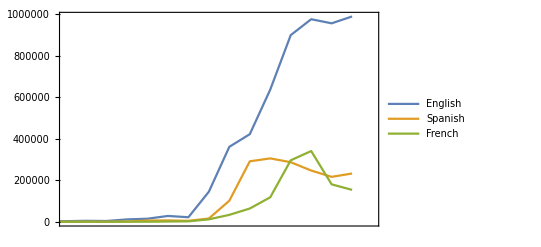

```mathematica
DateListPlot[Map[WikipediaData["Coronavirus","DailyPageHits",Language-> #]&,languages],PlotRange->{{DateObject[{2020,1,13},"Day","Gregorian",-6.],Today},All},PlotLegends->languages,ImageSize->400]
```

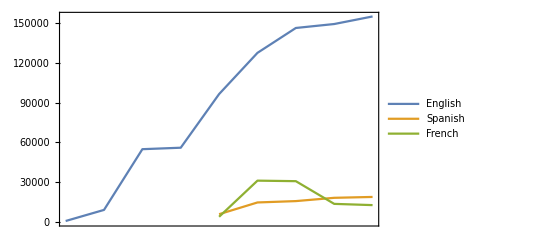

```mathematica
DateListPlot[Map[WikipediaData["Novel_coronavirus_(2019-nCoV)","DailyPageHits",Language-> #]&,languages],PlotRange->All,PlotLegends->languages,ImageSize->400]
```

## How quickly the virus spreads

One number that epidemiologists want to know is how many people one person with the virus tends to infect — known as R0, or R-naught. An R0 higher than 1 means that countermeasures, such as quarantine, will be needed to contain the pathogen’s spread.

On Thursday evening, after a meeting of an emergency committee responding to the outbreak, the World Health Organization (WHO) published an estimated R0 of 1.4 to 2.5. Other teams have since come up with slightly higher values. These estimates are similar to the R0 of SARS during the early stages of the 2002–03 outbreak, and of the novel strain of H1N1 influenza that caused a pandemic in 2009. But they are higher than R0 figures estimated during outbreaks of the Middle East respiratory syndrome (MERS) virus, a coronavirus similar to SARS.

But researchers caution that R0 estimates come with large uncertainties, because of gaps in the data, and the assumptions used to calculate the figure. They also point out that R0 is a moving target that changes over the course of an outbreak — as control measures are implemented — and varies from place to place. In the coming days, health authorities and researchers will be looking for signs that the steps the authorities have taken to stem transmission, such as the travel restrictions in Wuhan and other Chinese cities, have reduced the R0 there.

Another important unanswered question surrounding the virus’s spread is whether — and how extensively — people without symptoms can infect others. A study of a cluster of five infections in a family in Shenzhen identified a child who was infected with the virus but did not show any symptoms. If such asymptomatic cases are common and these individuals can spread the virus, then containing its spread will be much more difficult, researchers say. Few SARS cases were asymptotic, and this was key to controlling the virus.

## Conclusions

The underlying roots of newly emergent zoonotic diseases may lie in the parallel biodiversity crisis of massive species loss as a result of overexploitation of wild animal populations and the destruction of their natural habitats by increasing human populations.

People in cities should stop eating wild animals from wet markets. The younger generation is already on board and various high-profile Chinese people have been saying it. But sadly these markets are all over China and Vietnam. It is not just Wuhan.

## Other Resources

https://openwho.org/courses/introduction-to-ncov
https://www.who.int/health-topics/coronavirus